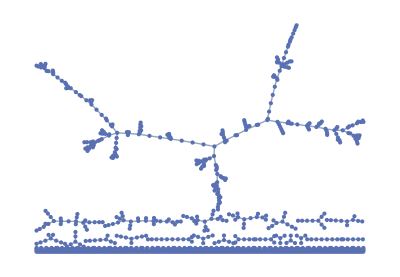

245

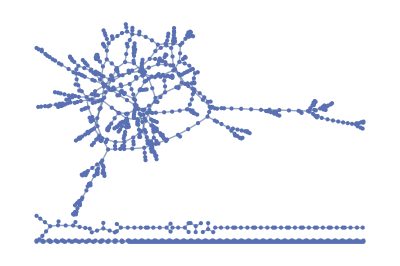

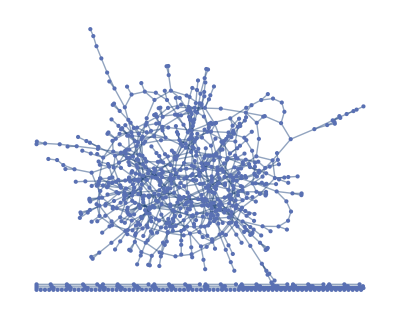

```mathematica
n = 1000;

theta1= 2;
theta2 = 5;
theta3 = 10;

g = RandomGraph[BernoulliGraphDistribution[n,1 / n + theta1*n^(-4/3)]]
Length[ConnectedComponents[g][[1]]]
g = RandomGraph[BernoulliGraphDistribution[n,1 / n + theta2*n^(-4/3)]]
g = RandomGraph[BernoulliGraphDistribution[n,1 / n + theta3*n^(-4/3)]]
```